# Logist Regression

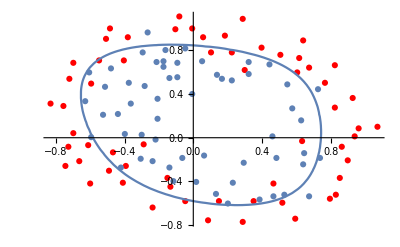

```mathematica
Clear["Global`*"]
```

```mathematica
Data =Import["D:\\machinelearning\\logistic regression\\ex2data2.txt","Data"];
```

```mathematica
f[lambda0_,order0_]:=Module[{lambda=lambda0,order=order0},
Exnum = Dimensions[Data]⟦1⟧;
Varnum = Dimensions[Data]⟦2⟧-1;
X = Data⟦;;,1;;2⟧;
y= Data⟦;;,3⟧;
costFunctionReg[theta_,X_,y_,lambda_]:= (-1/Exnum )*(y.Log[LogisticSigmoid[X.theta]]+(1-y).Log[1-LogisticSigmoid[X.theta]])+lambda/(2Exnum)*(theta.theta-theta[[1]]*theta[[1]]);
Features=DeleteDuplicates[Times@@@Tuples[Prepend[{x,z},1],order]];
Xextend=Table[Features/.{x->X⟦i,1⟧,z->X⟦i,2⟧},{i,1,Exnum}];
theta=Table[Subscript[θ, i],{i,Dimensions[Xextend]⟦2⟧}];
Result=FindMinimum[costFunctionReg[theta,Xextend,y,lambda],Table[Subscript[θ, i],{i,Dimensions[Xextend]⟦2⟧}],MaxIterations->1000];
thetaResult=theta/.Result⟦2⟧;
M=Mean[Boole[MapThread[Equal,{y,Boole[Thread[Xextend.thetaResult≥1]]}]]];
{Show[ListPlot[Select[Data,#[[3]]==0&][[;;,1;;2]],PlotStyle->Red],ListPlot[Select[Data,#[[3]]==1&][[;;,1;;2]]],ContourPlot[thetaResult.Features==0,{x,-1,1},{z,-1,1}]],
N[M]}]
```

### Regularization term λ = 1

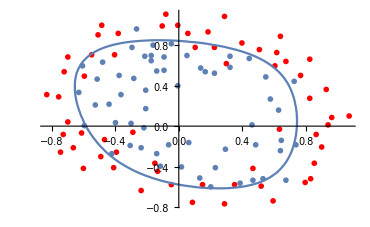
{-Graphics-,0.627119}

```mathematica
f[1,6]
```

### Regularization term λ = 0, no Regularization term will cause overfitting

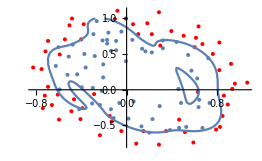
{-Graphics-,0.881356}

```mathematica
f[0,6]
```

### Regularization term λ = 100, too large Regularization parameter will cause underfitting

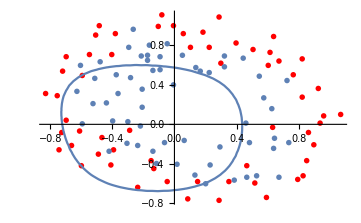
{-Graphics-,0.508475}

```mathematica
f[100,6]
```

### no Regularization term and the degree of polynomial = 4 gives a better fitting

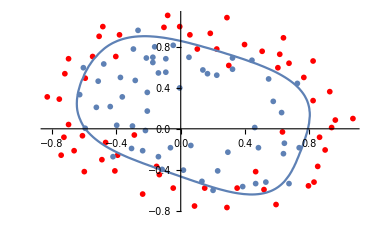
{-Graphics-,0.847458}

```mathematica
f[0,4]
```

### no Regularization term and the degree of polynomial = 2 , the accuracy is lower.

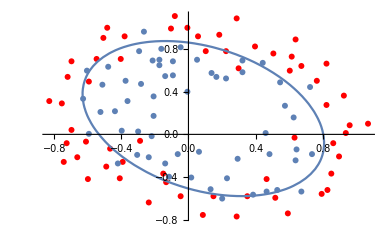
{-Graphics-,0.79661}

```mathematica
f[0,2]
```